```mathematica
Product[1-2^-i,{i,1,Infinity}]//N
```

0.288788095086602

```mathematica
Manipulate[Product[(1-2^i/(2^s Binomial[q,s]))/.s->10,{i,0,q-1}]//N,{q,10,101}]
```

```mathematica
Manipulate[(1-2^(q-1)/(2^s Binomial[q,s]))/.s->10//N,{q,10,101}]
```

# A

Instead of using multiple hash blocks, try bounding number of times to do Algo 4 using just 1 block.

P(random s-sparse vector not in V_i) ≥ 1-1/q
P(2s

```mathematica
Product[(n(1+eps)-i)/(n(1+eps)),{i,0,n-1}]/.eps->1/.n->5
```

189/625

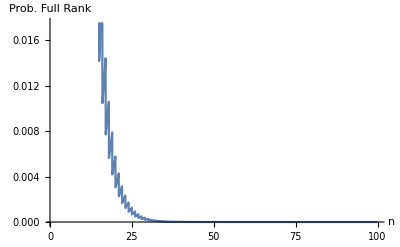

```mathematica
Plot[Product[(n(1+eps)-i)/(n(1+eps)),{i,0,n-1}]/.eps->1,{n,1,100},AxesLabel->{"n","Prob. Full Rank"}]
```

# B

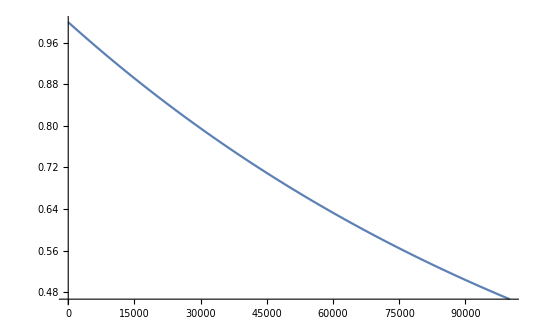

```mathematica
Plot[((1-2^k/p)^(r-1))^n/.r->5/.p->2^24/.k->5,{n,1,100000}]
```

# D

```mathematica
Table[i,{i,16,24}]
```

{16,17,18,19,20,21,22,23,24}

```mathematica
Manipulate[{(1-2^k/2^logp)^r,(1-(1-2^k/2^logp)^(r+1))-(1-(1-2^k/2^logp)^r)}//N,{r,1,100},{logp,Table[i,{i,16,24}]},{k,Table[i,{i,4,12}]}]
```

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.